```mathematica
DiffurStruc[func_,arg_,cprFunc_,ccur_]:={func'[arg]-ccur-cprFunc[func[arg]]==0};
DiffurIni[func_,InitialPoint_,InitialValue_]:={func[InitialPoint]==InitialValue};
Diffur[func_,arg_,cprFunc_,ccur_,InitialPoint_,InitialValue_]:=Flatten[
{DiffurStruc[func,arg,cprFunc,ccur],DiffurIni[func,InitialPoint,InitialValue]}];
```

```mathematica
CommonCPR[ccur_, cprFunc_, InitialPoint_,InitialValue_, {arg_,lowRange_,upperRange_}]:=
NDSolve[Diffur[γ,arg,cprFunc,ccur,InitialPoint,InitialValue],γ[arg],{arg,lowRange,upperRange}];
```

```mathematica
solution[ccur_, cprFunc_]:=Flatten[γ[t]/.CommonCPR[ccur, cprFunc,0,0,{t,0,1000π}]];
```

```mathematica
plots=Table[Plot[{(solution[i,(Sin[#]+a Sin[2#])&]/.t->1000π)/(1000π),i},{i,0,10}],{a,0,5,0.1}];
```

```mathematica
Export["F:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\plot.pdf",Show[plots,ImageSize->Large]]
```

F:\Google Disk\Учебные материалы\Физтех\Наука\plot.pdf

```mathematica
(*Сохранение результатов, папку path, для каждого графика отдельный "plot#.xls", где # - крит ток.*)
SaveResults[result_List,path_String]:=Module[{},
Map[Export[path<>"\\plot"<>ToString[#⟦1⟧⟦2⟧]<>".xls",Map[#[[1]]&,#]]&,result];
Export[path<>"\\currents.xls",Map[#[[1]][[2]]&,result]];];
```

```mathematica
(*Загрузка результатов. Лист с данными для графиков*)
LoadResults[path_String]:=Module[{currents},
currents=Flatten[Map[Flatten[#]&,Import[Evaluate[path<>"\\currents.xls"],"XLS"]]];
Map[Import[path<>"\\plot"<>ToString[#]<>".xls"]&,currents]];
```

```mathematica
SaveResults[result[[2]],"H:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\computation\\results\\result2"]
```

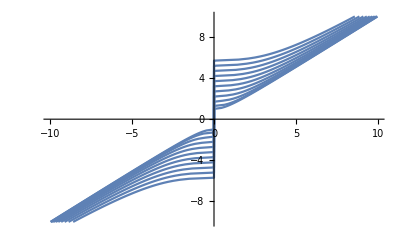

```mathematica
Show@Map[ListLinePlot[#]&,LoadResults["H:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\computation\\results\\result2"]]
```

```mathematica
Clear[result];result=ParallelTable[{{Flatten[(solution[i,(Sin[#]+a Sin[2#])&]/.t->3000)/3000][[1]],i},a},{a, 0,5,0.5},{i,-10,10,0.1}]//AbsoluteTiming
```

{106.728,{{{{-9.95,-10.},0.},{{-9.84945,-9.9},0.},{{-9.74892,-9.8},0.},{{-9.64839,-9.7},0.},{{-9.54784,-9.6},0.},{{-9.44731,-9.5},0.},{{-9.34671,-9.4},0.},{{-9.24616,-9.3},0.},{{-9.14558,-9.2},0.},183,{{9.14556,9.2},0.},{{9.24616,9.3},0.},{{9.34673,9.4},0.},{{9.44731,9.5},0.},{{9.54786,9.6},0.},{{9.64841,9.7},0.},{{9.74892,9.8},0.},{{9.84946,9.9},0.},{{9.95,10.},0.}},{1},7,{1},{1}}}
 |  |  |  |

```mathematica
Clear[result];result=ParallelTable[{{Flatten[(solution[i,(Sin[#]+a Sin[3#])&]/.t->3000)/3000][[1]],i},a},{a, 0,5,0.5},{i,-10,10,0.1}]//AbsoluteTiming
```

{153.288,{{{{-9.95,-10.},0.},{{-9.84945,-9.9},0.},{{-9.74892,-9.8},0.},{{-9.64839,-9.7},0.},{{-9.54784,-9.6},0.},{{-9.44731,-9.5},0.},{{-9.34671,-9.4},0.},{{-9.24616,-9.3},0.},{{-9.14558,-9.2},0.},183,{{9.14556,9.2},0.},{{9.24616,9.3},0.},{{9.34673,9.4},0.},{{9.44731,9.5},0.},{{9.54786,9.6},0.},{{9.64841,9.7},0.},{{9.74892,9.8},0.},{{9.84946,9.9},0.},{{9.95,10.},0.}},9,{1}}}
 |  |  |  |

```mathematica
SaveResults[result[[2]],"H:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\computation\\results\\result3"]
```

```mathematica
SaveResults[ParallelTable[{{Flatten[(solution[i,(Sin[2#]+a Sin[3#])&]/.t->3000)/3000][[1]],i},a},{a, 0,5,0.5},{i,-10,10,0.1}],"H:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\computation\\results\\result4"]
```

```mathematica
SaveResults[ParallelTable[{{Flatten[(solution[i,(a Sin[2#]+ Sin[3#])&]/.t->3000)/3000][[1]],i},a},{a, 0,5,0.5},{i,-10,10,0.1}],"H:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\computation\\results\\result5"]
```